## Various calculations related to Bragg scattering

### Alpha explicit on resonance with one state

```mathematica
FullSimplify[1/4(-1/I+-1/(2 d+I))(-1/-I+-1/(2 d-I))]
```

(1+d^2)/(1+4 d^2)

### Beta explicit on resonance with one state

```mathematica
FullSimplify[(-1/I--1/(2 d+I))(-1/-I--1/(2 d-I))]
```

(4 d^2)/(1+4 d^2)

```mathematica
FullSimplify[(-1/(2d+I)--1/(2 (d+1)+I))(-1/(2d-I)--1/(2 (d+1)-I))]
```

4/((1+4 d^2) (5+4 d (2+d)))

### Alpha explicit, very far away from both states

```mathematica
FullSimplify[1/4(-1/(2d+I)+-1/(2 d+I))(-1/(2d-I)+-1/(2 d-I))]
```

1/(1+4 d^2)

### Beta explicit, very far away from both states

```mathematica
FullSimplify[(-1/(2d+I)--1/(2 d+I))(-1/(2d-I)--1/(2 d-I))]
```

0

```mathematica
FullSimplify[(-1/(2d+I)--1/(2 (d+1)+I))(-1/(2d-I)--1/(2 (d+1)-I))]
```

4/((1+4 d^2) (5+4 d (2+d)))

### Definition of alpha and beta

```mathematica
ab[det_]:=Module[{d12,det2,det1,f1,f2,α,β},
d12=76/5.9;
det2 = det+d12/2.;
det1=det-d12/2.;
f1 = -1/(2(det1) + I);
f2 = -1/(2(det2)+I);

α=1/4(Abs[f1+f2])^2;
β=(Abs[f1-f2])^2;
{α,β}
]
```

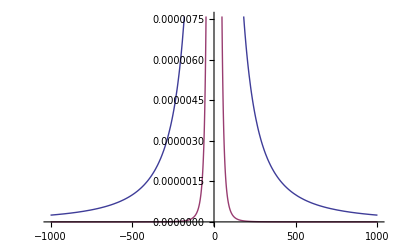

```mathematica
Plot[{ab[det][[1]],ab[det][[2]]},{det,-1000,1000}]
```

```mathematica
CCSum[K_]:=Module[{Cminus,Sites=20},
(*Print[K[[1]]];
Print[K[[2]]];
Print[K[[3]]];*)
Cminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)],
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];
Abs[Cminus]^2
]
SSum[K_]:=Module[{Sminus,Sites=20},
Sminus=Total[Flatten[
Table[
Table[
Table[Exp[I (K[[1]] i+K[[2]] j+K[[3]] k)](Mod[i+j+k,2]-1./2),
{i,1,Sites}],
{j,1,Sites}],
{k,1,Sites}]
]];

Abs[Sminus]^2
]
```

```mathematica
sigma[det_,K_]:=Module[{f1,f2,α,β},

f1=-1/(2 (det-12.9/2)+I);
f2=-1/(2(det+12.9/2)+I);

α=1/4(Abs[f1+f2])^2;
β=(Abs[f1-f2])^2;
(α CCSum[K]+β SSum[K])
]
```

### KBragg = π, π, π (Andor2) KDiffuse = π { sin30, cos30 - cosθ, sinθ } (Andor1) θ is the angle that we use between the Bragg beam and lattice 2 retro.

```mathematica
KBragg={π,π,-π};
θ=ArcTan[0.5/8.75];
KDiffuse={π/2,π((√3)/2-Cos[θ]),π Sin[θ]};
KDiffuse={-2.4908,0.66049,0.2623};
```

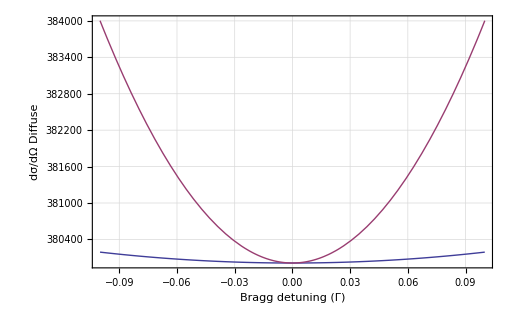

```mathematica
Plot[{sigma[det,KBragg],sigma[det,KDiffuse] sigma[0.,KBragg]/sigma[0.,KDiffuse]},{det,-.1,.1},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","dσ/dΩ Diffuse"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

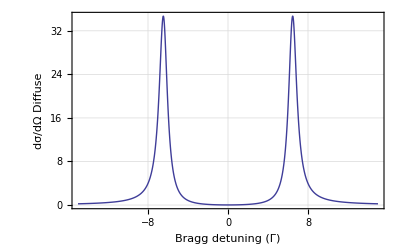

```mathematica
Plot[{sigma[det,KDiffuse]},{det,-15,15},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","dσ/dΩ Diffuse"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

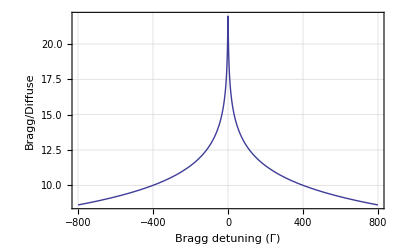

```mathematica
Plot[{Log[sigma[det,KBragg]/sigma[det,KDiffuse]]},{det,-800,800},
PlotRange->All,
GridLines->Automatic,
Frame->True,FrameLabel->{"Bragg detuning (Γ)","Bragg/Diffuse"},
LabelStyle->Directive[FontFamily->"Times",FontSize->18,Bold],
ImageSize->{400}
]
```

```mathematica
ab[0.]
```

{0.0000358868,0.0238187}

```mathematica
CCSum[KBragg]
SSum[KBragg]
```

0

1.6×10^7

```mathematica
CCSum[KDiffuse]
SSum[KDiffuse]
```

0.755545

0.00339276

```mathematica
ab[-100000]
```

{2.5×10^-11,4.14823×10^-19}

## Coherent - Incoherent fractions

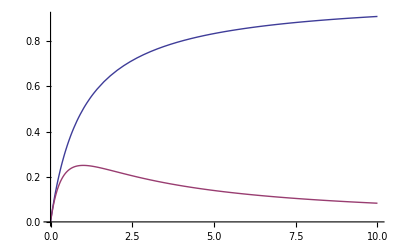

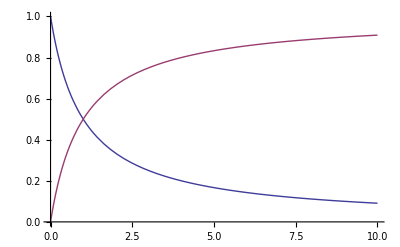

```mathematica
total[S_]:=S/(1+S)
coh[S_]:=S/(1+S)^2
inc[S_]:=S^2/(1+S)^2
Plot[{total[S],coh[S]},{S,0,10}]
Plot[{coh[S]/total[S], inc[S]/total[S]},{S,0,10}]
```

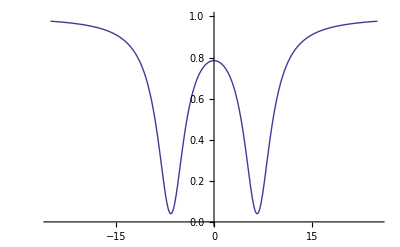

```mathematica
Plot[ 1/(1+2*12(1/(1+4(det-6.6)^2)+1/(1+4(det+6.6)^2))),{det,-25,25},PlotRange->{0,1}]
```